# Kolokvij (računalniški praktikum)

## 14. januar 2019

## Navodila

Naloge rešujte samostojno. Uporabljati smete svoje zapiske in dokumentacijo za Mathematico. Brskanje po internetu ni dovoljeno (in vam ne bo koristilo).

Če kaj ni jasno, vprašajte asistentko ali asistenta.

Pri vsaki nalogi rešitve zapišite v razdelek “Rešitve”. Rešitve opremite z dovolj besedila, da bomo razumeli vašo resitev. Na primer, če je vprašanje “Izračunajte vrednost y, pri kateri ...”, potem mora biti iz vaše rešitve jasno razvidno, katero vrednost y ste izračunali.

Rešitev ne računajte na roko na papirju, ampak z Mathematico, saj je bistvo preverjanja vaše znanje Mathematice.

Ročno kopiranje rezultatov iz enega računa v naslednjega kaže na slab stil. Za polno število točk naj bodo rešitve napisane tako, da uporabniku ni treba ničesar kopirati ali prepisovati na roko. (Seveda pa morate na roko skopirati vhodne podatke iz besedila naloge.)

## 1. naloga

Naloga 1.1: Poiščite taki celi števili m in n, da bo veljalo 42 m+2019 n==3

Naloga 2.1: Izračunajte na deset decimalk natančno (v pomoč naj vam bo funkcija FromContinuedFraction):

1+1/(2+1/(3+1/(⋱_(+1/2019))))

Naloga 1.3: Izračunajte limito lim_(x→0) (e^(x^2-1))/(cos(x)).

### Rešitve

#### Prva podnaloga

```mathematica
FindInstance[42*m+2019*n == 3,{m,n},Integers]
```

{{m→625,n→-13}}

#### Druga podnaloga

```mathematica
NSolve[1+1/(2+1/(3+1/(⋱_(+1/2019)))),10]
```

{{⋱_(1/2019)→-0.3}}

#### Tretja podnaloga

```mathematica
Limit[(E^{x^2-1})/Cos[x],x-> 0] // First
```

1/ⅇ

## 2. naloga

Naloga 2.1: Narišite implicitno podano krivuljo |x|^(2/3)+|y|^(2/3)=1 na območju [-1,1]×[-1,1].

Naloga 2.2: Z ukazom Manipulate prikažite, kako se spreminja graf implicitne krivulje |x|^p+|y|^p==1 za vrednosti parametra p∈[0,4].

Naloga 2.3: Pri kateri vrednosti p točka (1/3,1/3) leži na grafu krivulje?

### Rešitve

#### Prva podnaloga

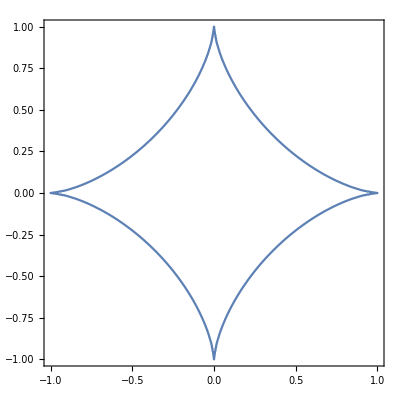

```mathematica
ContourPlot[Abs[x]^{2/3}+Abs[y]^{2/3}==1,{x,-1,1},{y,-1,1}]
```

#### Druga podnaloga

```mathematica
Manipulate[ContourPlot[Abs[x]^p+Abs[y]^p==1,{x,-1,1},{y,-1,1}],{p,0,4}]
```

#### Tretja podnaloga

```mathematica
p /. Solve[Abs[1/3]^p+Abs[1/3]^p==1,p,Reals]  // First
```

Log[2]/Log[3]

## 3. naloga

Naj bo p(x) =a x^2+ b x+c. Za nekatere vrednosti koeficientov a, b, c se zaporedje  p(1), p(2), p(3), ... začne s praštevili. Na primer, če je p(x) = x^2+3x+1, dobimo zaporedje, katerih prvih pet členov so praštevila:

```mathematica
Table[x^2+3*x+1,{x,1,20}]
```

{5,11,19,29,41,55,71,89,109,131,155,181,209,239,271,305,341,379,419,461}

Poiščite take vrednosti a, b, c, da bodo  p(1), p(2), p(3), ..., p(20) praštevila. Rešitev lahko dobite takole:

Naloga 3.1: Definirate funkcijo dobraQ[{a,b,c}],  ki vrne True, če so vrednosti polinoma a x^2+b x+c praštevila za vsa naravna števila 1≤x≤20. Namig: kaj naredi Apply[And, {p,q,r,s}]?

Naloga 3.2: Z ukazoma Table in Flatten definirajte seznam l vseh trojic naravnih števil {a,b,c}, kjer velja 1≤a,b,c≤25. Pazite, da l ne bo seznam seznamov seznamov seznamov, ampak le seznam seznamov.

Naloga 3.3: Z ukazom Select iz seznama l izberete tiste trojice {a,b,c}, pri katerih dobraQ vrne True.

### Rešitve

#### Prva podnaloga

```mathematica
dobraQ[{a_,b_,c_}]:= Apply[And,Table[PrimeQ[a*x^2+b*x+c],{x,20}]]
```

#### Druga podnaloga

```mathematica
trojice :=Flatten[Table[Table[Table[{a,b,c},{c,1,25}],{b,1,25}], {a,1,25}],2]
```

#### Tretja podnaloga

```mathematica
Select[trojice,dobraQ]
```

{{3,3,23}}